## Ashcroft’s Model

```mathematica
M[x_,y_,z_]:=({{(y^2+x^2+z^2), 0.0179, 0.0179, 0.0562}, {0.0179, ((-1+y)^2+(-1+x)^2+(-1+z)^2), 0.0562, 0.0179}, {0.0179, 0.0562, ((-1+y)^2+(-1+x)^2+(1+z)^2), 0.0179}, {0.0562, 0.0179, 0.0179, (y^2+(-2+x)^2+z^2)}});
w[x_,y_,z_]:=Sqrt[x^2+z^2+y^2];
```

```mathematica
data1=Diagonal[Table[Eigenvalues[M[x,0.5,z]],{x,1,0.5,-0.01},{z,0,0.5,0.01}]];
datak1=Diagonal[Table[Sqrt[(x-1)^2+z^2],{x,1,0.5,-0.01},{z,0,0.5,0.01}]];
data2=Diagonal[Diagonal[Table[Eigenvalues[M[x,y,z]],{x,0.5,0,-0.01},{y,0.5,0,-0.01},{z,0.5,0,-0.01}]]];
datak2=Diagonal[Diagonal[Table[Sqrt[(x-0.5)^2+(y-0.5)^2+(z-0.5)^2],{x,0.5,0,-0.01},{y,0.5,0,-0.01},{z,0.5,0,-0.01}]]];
data3=Table[Eigenvalues[M[x,0,0]],{x,0,0.5,0.01}];
datak3=Table[Sqrt[x^2],{x,0,0.5,0.01}];
data31=Table[Eigenvalues[M[x,0,0]],{x,0.5,1,0.01}];
datak31=Table[Sqrt[(x-0.5)^2],{x,0.5,1,0.01}];
data4=Table[Eigenvalues[M[1,y,0]],{y,0,0.5,0.01}];
datak4=Table[Sqrt[y^2],{y,0,0.5,0.01}];
data5=Diagonal[Table[Eigenvalues[M[x,y,0]],{x,1,0.75,-0.005},{y,0.5,0.75,0.005}]];
datak5=Diagonal[Table[Sqrt[(x-1)^2+(y-0.5)^2],{x,1,0.75,-0.005},{y,0.5,0.75,0.005}]];
datak=Join[-1.55+datak1,-0.85+datak2,datak3,datak31+0.5,datak4+1,datak5+1.5]//MatrixForm;
data=Join[data1,data2,data3,data31,data4,data5]//MatrixForm;
tick0={-1.55,"W"};
tick1={-0.85,"L"};
tick2={0,"Γ"};
tick3={1,"X"};
tick4={1.5,"W"};
tick5 = {1.85,"Κ"};
```

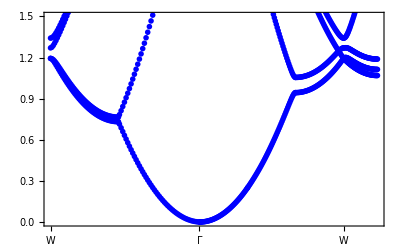

```mathematica
p1=ListPlot[Table[{datak[[1,n]],data[[1,n,i]]},{n,306},{i,4}],PlotRange->1.5,Frame->True,Axes->{True,False},FrameTicks->{{tick0,tick1,tick2,tick3,tick4,tick5},Automatic},PlotStyle->{Blue},ImageSize->Full]
```

## Free Electrons

```mathematica
Mf[x1_,y1_,z1_]:=({{(x1)^2+(y1)^2+(z1)^2, 0, 0, 0}, {0, ((-1+y1)^2+(-1+x1)^2+(-1+z1)^2), 0, 0}, {0, 0, ((-1+y1)^2+(-1+x1)^2+(1+z1)^2), 0}, {0, 0, 0, (y1^2+(-2+x1)^2+z1^2)}});
wf[x1_,y1_,z1_]:=Sqrt[x1^2+y1^2+z1^2];
```

```mathematica
dataf1=Diagonal[Table[Eigenvalues[Mf[x1,0.5,z1]],{x1,1,0.5,-0.01},{z1,0,0.5,0.01}]];
datafk1=Diagonal[Table[Sqrt[(x1-1)^2+z1^2],{x1,1,0.5,-0.01},{z1,0,0.5,0.01}]];
dataf2=Diagonal[Diagonal[Table[Eigenvalues[Mf[x1,y1,z1]],{x1,0.5,0,-0.01},{y1,0.5,0,-0.01},{z1,0.5,0,-0.01}]]];
datafk2=Diagonal[Diagonal[Table[Sqrt[(x1-0.5)^2+(y1-0.5)^2+(z1-0.5)^2],{x1,0.5,0,-0.01},{y1,0.5,0,-0.01},{z1,0.5,0,-0.01}]]];
dataf3=Table[Eigenvalues[Mf[x1,0,0]],{x1,0,0.5,0.01}];
datafk3=Table[Sqrt[x1^2],{x1,0,0.5,0.01}];
dataf31=Table[Eigenvalues[Mf[x1,0,0]],{x1,0.5,1,0.01}];
datafk31=Table[Sqrt[(x1-0.5)^2],{x1,0.5,1,0.01}];
dataf4=Table[Eigenvalues[Mf[1,y1,0]],{y1,0,0.5,0.01}];
datafk4=Table[Sqrt[y1^2],{y1,0,0.5,0.01}];
dataf5=Diagonal[Table[Eigenvalues[Mf[x1,y1,0]],{x1,1,0.75,-0.005},{y1,0.5,0.75,0.005}]];
datafk5=Diagonal[Table[Sqrt[(x1-1)^2+(y1-0.5)^2],{x1,1,0.75,-0.005},{y1,0.5,0.75,0.005}]];
datafk=Join[-1.55+datafk1,-0.85+datafk2,datafk3,datafk31+0.5,datafk4+1,datafk5+1.5]//MatrixForm;
dataf=Join[dataf1,dataf2,dataf3,dataf31,dataf4,dataf5]//MatrixForm;
tick0={-1.55,"W"};
tick1={-0.85,"L"};
tick2={0,"Γ"};
tick3={1,"X"};
tick4={1.5,"W"};
tick5 = {1.85,"Κ"};
```

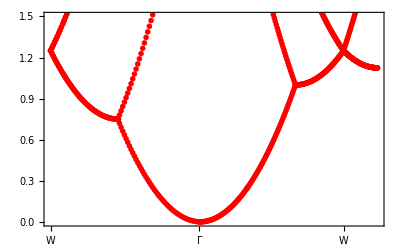

```mathematica
p2=ListPlot[Table[{datafk[[1,m]],dataf[[1,m,j]]},{m,306},{j,4}],PlotRange->1.5,Frame->True,FrameTicks->{{tick0,tick1,tick2,tick3,tick4,tick5},Automatic},Axes->{True,False},PlotStyle->{Red},ImageSize->Full]
```

## Final Plot

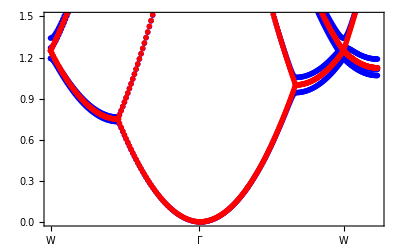

```mathematica
Show[p1,p2]
```